## density matrix |ψ(α,ϕ)> = Sin[α]|HH> + exp(iϕ)Cos[α] |VV> ρ = |ψ><ψ|

```mathematica
(* Basis: {HH,HV,VH,VV} *)
(* 
|α> = Sin[α]|H> + Cos[α]|V>,
|β> = Sin[β]|H> + Cos[β]|V>
*)
αβ[α_,β_]:= Normalize[{Sin[α]*Sin[β],Sin[α]*Cos[β],Cos[α]*Sin[β],Cos[α]*Cos[β]}]
(* density matrix of a quantum state Sin[α] |HH> + Cos[α]Exp[I*ϕ] |VV> *)
dm[ϕ_,α_]:={{Sin[α]^2,0,0,Sin[α]*Cos[α]*Exp[-I*ϕ]},{0,0,0,0},{0,0,0,0},{Sin[α]*Cos[α]*Exp[I*ϕ],0,0,Cos[α]^2}};
dm[ϕ_]:= dm[ϕ,π/4];
(* dm[ϕ_]:=1/2{{1,0,0,Exp[-I*ϕ]},{0,0,0,0},{0,0,0,0},{Exp[I*ϕ],0,0,1}}; *)
dm[ϕ,α] // MatrixForm
dm[ϕ] //MatrixForm
```

(Sin[α]^2 | 0 | 0 | ⅇ^(-ⅈ ϕ) Cos[α] Sin[α]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(ⅈ ϕ) Cos[α] Sin[α] | 0 | 0 | Cos[α]^2)

(1/2 | 0 | 0 | ⅇ^(-ⅈ ϕ)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(ⅈ ϕ)/2 | 0 | 0 | 1/2)

```mathematica
(* detection probability: density matrix ρ, measurement angles α and β *)
PDet[ρ_,α_,β_]:= αβ[α,β].ρ.αβ[α,β];
(* expectation value *)
EValue[ρ_,α_,β_]:= αβ[α,β].ρ.αβ[α,β] + αβ[α+π/2,β+π/2].ρ.αβ[α+π/2,β+π/2] -αβ[α+π/2,β].ρ.αβ[α+π/2,β]-αβ[α,β+π/2].ρ.αβ[α,β+π/2];
```

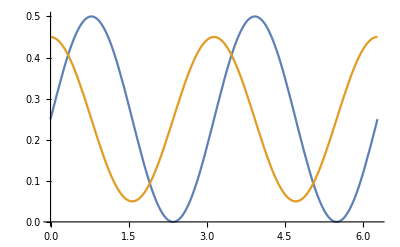

```mathematica
Plot[{PDet[dm[0],π/4,β],PDet[0.8*dm[π/4]+1/4*IdentityMatrix[4]*0.2,0,β]},{β,0,2π}]
```

```mathematica
(* Bell's inequality *)
SValue[ρ_]:=Chop[Evaluate[EValue[ρ,α1,β1]+ EValue[ρ,α2,β1] + EValue[ρ,α2,β2] -EValue[ρ,α1,β2] /.{α1->0,α2->45/180*π,β1->22.5/180*π,β2->67.5/180*π}]]
(* rotate measurement directions by Δαβ *)
SValue[ρ_,Δα_,Δβ_]:=Chop[Evaluate[EValue[ρ,α1+Δα,β1+Δβ]+ EValue[ρ,α2+Δα,β1+Δβ] + EValue[ρ,α2+Δα,β2+Δβ] -EValue[ρ,α1+Δα,β2+Δβ] /.{α1->0,α2->45/180*π,β1->22.5/180*π,β2->67.5/180*π}]]
```

## calculate S from count rates measurements in 2 basis on signal and idler photons - α1 = {0°,90°}, α2 = {45°,45°+90°} - β1 = {22.5°,22.5°+90°}, β2 = {67.5°,67.5+90°} with two detectors (one on each side) 4*4 measurements have to be done

```mathematica
(* measurement basis *)
αbasis={α->0,α->45/180*π};
βbasis ={β->22.5/180*π,β->67.5/180*π}  //Hold // Rationalize // ReleaseHold;
```

```mathematica
bellmeasurements={{{αp->0,βp->π/8,Npp->Npp1},{αp->0,βm->(5 π)/8,Npm->Npm1},{αm->π/2,βp->π/8,Nmp->Nmp1},{αm->π/2,βm->(5 π)/8,Nmm->Nmm1}},{{αp->0,βp->(3 π)/8,Npp->Npp2},{αp->0,βm->(7 π)/8,Npm->Npm2},{αm->π/2,βp->(3 π)/8,Nmp->Nmp2},{αm->π/2,βm->(7 π)/8,Nmm->Nmm2}},{{αp->π/4,βp->π/8,Npp->Npp3},{αp->π/4,βm->(5 π)/8,Npm->Npm3},{αm->(3 π)/4,βp->π/8,Nmp->Nmp3},{αm->(3 π)/4,βm->(5 π)/8,Nmm->Nmm3}},{{αp->π/4,βp->(3 π)/8,Npp->Npp4},{αp->π/4,βm->(7 π)/8,Npm->Npm4},{αm->(3 π)/4,βp->(3 π)/8,Nmp->Nmp4},{αm->(3 π)/4,βm->(7 π)/8,Nmm->Nmm4}}};
```

```mathematica
(* expectation value and error of expectation value p:+, m:- *)
EValue[{Npp_,Npm_,Nmp_,Nmm_}]:= (Npp+Nmm -Nmp-Npm)/(Npp+Nmm+Nmp+Npm);
ΔEValue[{Npp_,Npm_,Nmp_,Nmm_}]:= Evaluate[Sqrt[(D[EValue[{Npp,Npm,Nmp,Nmm}],Npp]*Sqrt[Npp])^2 + (D[EValue[{Npp,Npm,Nmp,Nmm}],Nmm]*Sqrt[Nmm])^2 + (D[EValue[{Npp,Npm,Nmp,Nmm}],Npm]*Sqrt[Npm])^2 + (D[EValue[{Npp,Npm,Nmp,Nmm}],Nmp]*Sqrt[Nmp])^2]]
```

```mathematica
SValue[{Npp1_,Npm1_,Nmp1_,Nmm1_,Npp2_,Npm2_,Nmp2_,Nmm2_,Npp3_,Npm3_,Nmp3_,Nmm3_,Npp4_,Npm4_,Nmp4_,Nmm4_}]:=Evaluate[(EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[1]]]) - (EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[2]]]) +(EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[3]]]) +(EValue[{Npp,Npm,Nmp,Nmm}] /. Flatten[bellmeasurements[[4]]])];
tmp={Npp1,Nmm1,Npm1,Nmp1,Npp2,Nmm2,Npm2,Nmp2,Npp3,Nmm3,Npm3,Nmp3,Npp4,Nmm4,Npm4,Nmp4};
ΔSValue[{Npp1_,Npm1_,Nmp1_,Nmm1_,Npp2_,Npm2_,Nmp2_,Nmm2_,Npp3_,Npm3_,Nmp3_,Nmm3_,Npp4_,Npm4_,Nmp4_,Nmm4_}]:=
Evaluate[Sqrt[Total[Map[Function[x,D[SValue[{Npp1,Nmm1,Npm1,Nmp1,Npp2,Nmm2,Npm2,Nmp2,Npp3,Nmm3,Npm3,Nmp3,Npp4,Nmm4,Npm4,Nmp4}],x]^2*x],tmp] 
]
]
]
```

```mathematica
(* mean number of coincidences for a state dm *)
μbell = αβ[α,β].dm[0].αβ[α,β] /. Flatten[bellmeasurements /.{αp->α,βp->β,αm->α,βm->β},1] //N
```

{0.426777,0.0732233,0.0732233,0.426777,0.0732233,0.426777,0.426777,0.0732233,0.426777,0.0732233,0.0732233,0.426777,0.426777,0.0732233,0.0732233,0.426777}

```mathematica
testcoinc=Map[Function[x,RandomVariate[PoissonDistribution[x]]] ,μbell*1500+120]
SValue[testcoinc] //N
ΔSValue[testcoinc] //N
```

{881,224,244,824,250,866,845,227,897,248,218,853,892,253,249,883}

2.27174

0.0425097